```mathematica
AlphaTest[x_]:=0≤x≤25
TextCode[text_]:=Select[
					ToCharacterCode[
						ToUpperCase[text]]-65,AlphaTest];
FromCode[textcode_]:=FromCharacterCode[textcode+65];


testo="001 FIOPPQNTPN BUUGGMOCYY JFMDVUUDEY ICLDYVITVL IJMMAAPYGF
            051 MOEHFKFMTV ZEIFMETVBV KDDNPFVKOI YHJZIVNRUI DCZMBKYAZX
            101 AMPEIZYEVW QOKDAPJUOK VTRKQGCZDH LFVIOIAVDM ZXHVLTJEJP
            151 EVSZUDMRUJ JUDRRCYNZJ NRJENKDTHG YJEVLRHHOK PTGLBZTJNS
            201 LINZJNVYUG ZBIBZUNFIO RNKVCHEAAU GZWEELTVMV NGPQGCVLRN
            251 WZCZCBUVZJ NIBUYMVGIT PENVYIILHN VYAYSQXROT BSYXRCAAUE
            301 YZMIGAEYZJ RTHDDQUAEZ YNVXOAKEDG MOCYYNKVTH AYDELUNUJJ";
ciphertext=TextCode[testo];

CoincidenceIndex[testo_]:=
If[
StringQ[testo],
(*THEN*)
CoincidenceIndex[TextCode[testo]],
(*ELSE*)
Module[{n,freqs},
(
n=Length[testo];
freqs=Map[Count[testo,#]&,Range[0,25]];
N[Plus@@(freqs(freqs-1)/(n (n-1)))]
)]
]


CoincidenceIndex[ciphertext]
```

0.0424069

```mathematica
?Pattern
```

```mathematica
message=Import["http://www.repubblica.it"];
Italian=Import["http://www.corriere.it"];
English=Import["http://www.nytimes.com"];
```

```mathematica
CoincidenceIndex[message]
CoincidenceIndex[Italian]
CoincidenceIndex[English]
CoincidenceIndex[random=RandomInteger[{0,25},3000]]
```

0.0762738

0.07497

0.0645191

0.0384659

```mathematica
StringTake[message,10]
```

Abbonati

```mathematica
TableForm@(tab=Table[
Map[CoincidenceIndex[Take[#,len]]&,{TextCode@message,TextCode@Italian,TextCode@English,random}],
{len,10,200,10}])
```

0.0444444 | 0.0444444 | 0.0444444 | 0.0444444
0.0789474 | 0.0789474 | 0.0473684 | 0.0421053
0.0988506 | 0.0804598 | 0.0528736 | 0.0436782
0.0807692 | 0.0897436 | 0.0641026 | 0.0423077
0.077551 | 0.0832653 | 0.0636735 | 0.0383673
0.0751412 | 0.0774011 | 0.0700565 | 0.0355932
0.0753623 | 0.0766046 | 0.0716356 | 0.0409938
0.0762658 | 0.0756329 | 0.0781646 | 0.0389241
0.074407 | 0.0741573 | 0.0754057 | 0.0367041
0.0753535 | 0.0739394 | 0.0743434 | 0.0371717
0.0752294 | 0.0750626 | 0.0705588 | 0.0376981
0.072549 | 0.0735294 | 0.0689076 | 0.0379552
0.0729875 | 0.0754919 | 0.0683363 | 0.0373286
0.0742035 | 0.076259 | 0.0717369 | 0.0366906
0.0741834 | 0.0749888 | 0.0721253 | 0.0369575
0.0725629 | 0.0746069 | 0.0706761 | 0.0372642
0.071354 | 0.0760181 | 0.0707275 | 0.0374521
0.0705152 | 0.0758535 | 0.0703911 | 0.0378647
0.0705653 | 0.0762462 | 0.0683375 | 0.0374826
0.0705528 | 0.0771357 | 0.0670854 | 0.0376884

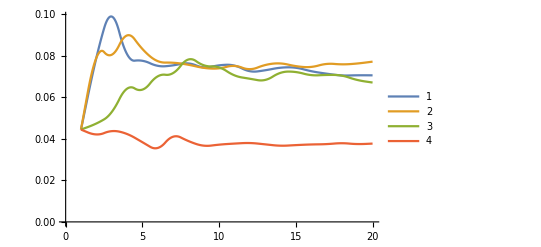

```mathematica
ListLinePlot[Transpose@tab,InterpolationOrder->2,PlotLegends->Automatic]
```

```mathematica
StringTake[Italian,10]
```

desktop

```mathematica
g=#+#& 
g[2]
```

#1+#1&

4

```mathematica
CoincidenceIndex[StringTake[message,10]]
```

0.0714286

```mathematica
RandomInteger[{0,25},300]
```

{15,21,7,9,3,19,19,2,4,20,4,3,14,18,1,15,17,16,6,5,7,24,22,4,7,11,20,14,11,21,4,8,20,21,5,23,6,11,22,13,3,21,25,2,10,5,21,7,21,9,7,20,9,7,25,19,18,16,15,22,8,3,25,8,7,22,7,4,2,24,14,4,25,12,10,3,4,9,19,19,11,9,15,5,3,16,20,10,0,19,12,18,18,17,10,7,14,5,11,10,2,1,8,25,11,0,16,8,24,8,18,24,22,9,9,24,16,14,15,22,21,15,4,22,23,11,9,21,22,10,12,22,14,23,9,10,2,13,11,22,6,10,24,20,25,11,22,9,12,9,14,1,0,6,4,12,11,15,6,18,19,5,23,1,21,13,13,0,24,3,15,23,0,24,4,21,22,25,21,13,4,5,20,5,5,8,10,14,18,10,17,18,18,14,10,9,19,18,20,24,24,7,20,17,6,8,7,16,18,25,10,18,8,11,24,13,12,0,2,1,14,4,25,24,19,19,1,15,19,13,6,8,12,19,5,20,20,21,0,5,24,24,24,9,18,7,10,20,15,5,19,14,6,8,22,22,11,7,6,1,16,8,3,19,14,13,8,11,23,24,12,14,19,18,9,0,7,13,9,18,17,2,14,5,7,21,25,6,16,3,17,9,8,20,25,12,2,9,3,3}

```mathematica
TextCode[StringTake[message,50]]
```

{0,1,1,14,13,0,19,8,12,4,13,20,2,4,17,2,0}

```mathematica
CoincidenceIndex[testo_,trunc_,n_]:=
If[
StringQ[testo],
(*THEN*)
CoincidenceIndex[TextCode[testo],trunc,n],
(*ELSE*)
Module[{ntesto,tfreqs},
(
ntesto=Take[testo,n];
tfreqs=Take[Sort[Map[Count[ntesto,#]&,Range[0,25]]],-trunc];
N[Plus@@(tfreqs(tfreqs-1)/(n (n-1)))]
)]
]
```

```mathematica
n=10
testo=Take[TextCode[message],n];

trunc=5

freqs=Map[Count[testo,#]&,Range[0,25]]
Sort[freqs]
tfreqs=Take[Sort[freqs],-trunc]

N[Plus@@(tfreqs(tfreqs-1)/(n (n-1)))]
```

10

5

{2,2,0,0,1,0,0,0,1,0,0,0,1,1,1,0,0,0,0,1,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,2,2}

{1,1,1,2,2}

0.0444444

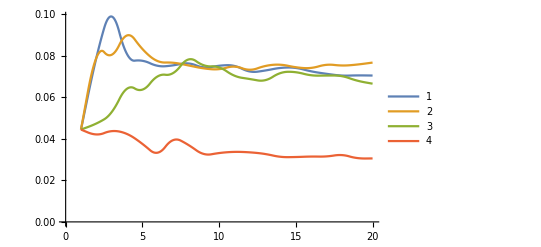

```mathematica
TableForm@(tab=Table[
Map[CoincidenceIndex[#,15,len]&,{TextCode@message,TextCode@Italian,TextCode@English,random}],
{len,10,200,10}]);
ListLinePlot[Transpose@tab,InterpolationOrder->2,PlotLegends->Automatic]
```

```mathematica
distances=Table[
ngrams=Partition[ciphertext,bsize,1];
repetitions=Select[SortBy[Tally[ngrams],Last],#[[2]]>1&];
reps=Map[First,repetitions];
positions=Map[Map[#[[1]]&,Position[ngrams,#]]&,Take[reps,-3];


Drop[positions,1]-Drop[positions,-1],{bsize,3,6}];
GCD@@Flatten[distances]
```

{{35,55},{315},{315},{315}}

5

```mathematica
Flatten[{{1,2},{3,4}}]
```

{1,2,3,4}

```mathematica
blocks=Transpose[Partition[ciphertext,7]];
Map[CoincidenceIndex,blocks]
```

{0.084898,0.0669388,0.0865306,0.0726531,0.077551,0.0865306,0.0857143}